```mathematica
csvPath = "M:\\JI Courses\\Sophomore_Year\\2019_Spring\\VE401\\Proj2\\Codes\\6\\data2019.xlsx";
SystemOpen@csvPath
Data = Import[csvPath];
Count1=Data[[1]][[2;;-16]];
Count2 = Tally[Count1[[All,2]]]
```

{{2.,22},{3.,18},{6.,5},{4.,11},{5.,7},{1.,16},{7.,2},{0.,8},{9.,1}}

```mathematica
(*The fit done by Mathematica*)
Needs["HypothesisTesting`"];
TestData = Join[Table[0,{i,1,8}],Table[1,{i,1,16}],Table[2,{i,1,22}],Table[3,{i,1,18}],Table[4,{i,1,11}],Table[5,{i,1,7}],Table[6,{i,1,5}],Table[7,{i,1,2}],Table[9,{i,1,1}]];
PearsonChiSquareTest[TestData,PoissonDistribution[k1],{"FittedDistributionParameters","DegreesOfFreedom","TestDataTable"}]
```

{{k1→2.73333},4, | Statistic | P-Value
Pearson χ^2 | 2.23499 | 0.692629}

```mathematica
(*The fit done considering Pearson Criteria 3.1.2*)
Count2= {{0,8},{1,16},{2,22},{3,18},{4,11},{5,7},{6,5},{7,2},{8,0},{9,1}};
k2 = 0;
n=31+28+31;
For[i=1,i≤10,i++,k2 = k2+Count2[[i,1]]*Count2[[i,2]]];
k2 = N[k2/n]
```

2.73333

```mathematica
e= N[Exp[1]];
CRV={};
For[i=0,i≤9,i++,CRV =Insert[CRV,e^(-k2)*k2^i/Factorial[i],-1]];
CRV
```

{0.0650023,0.177673,0.24282,0.221236,0.151178,0.0826438,0.0376488,0.014701,0.00502283,0.00152545}

```mathematica
ExpectedE = {};
For[i=1,i≤10,i++,ExpectedE =Insert[ExpectedE,n*CRV[[i]],-1]];
ExpectedE
```

{5.8502,15.9906,21.8538,19.9112,13.606,7.43794,3.38839,1.32309,0.452055,0.137291}

```mathematica
(*We see that the Pearson Criteria 3.1.2 is not satisfied, therefore we merge the last 4 categories and obtain the following*)
Count3 = {{0,8},{1,16},{2,22},{3,18},{4,11},{5,7},{6,8}};
NewCRV={0.06500225396303454,0.17767282749896107,0.2428195309152468,0.22123557261166932,0.15117764128464067,0.08264377723560358,0.037648831851774964+0.01470097243735975+0.007098592201709374};
NewExpectedE={5.850202856673108,15.990554474906496,21.853757782372213,19.91120153505024,13.60598771561766,7.4379399512043225,3.3883948666597465+1.3230875193623775+0.6388732981538436};
NewObservedE= {8,16,22,18,11,7,8};
(*The Degree of Fredom is found by*)
DegreesOfFreedom = Length[NewExpectedE]-1-1
```

5

```mathematica
(*The Pearson Statistic is found by*)
Stat = 0;
For[i=1,i≤7,i++,Stat=Stat+(NewObservedE[[i]]-NewExpectedE[[i]])^2/NewExpectedE[[i]]];
Stat
```

2.81152

```mathematica
(*Fix alpha=0.05, we test the null hypothesis, and fail to reject it*)
Solve[CDF[ChiSquareDistribution[DegreesOfFreedom],x]==0.95,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→11.0705}}

```mathematica
(*The P value is found by:*)
PValue = 1-CDF[ChiSquareDistribution[DegreesOfFreedom],Stat]
```

0.729016

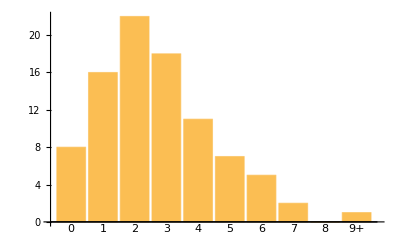

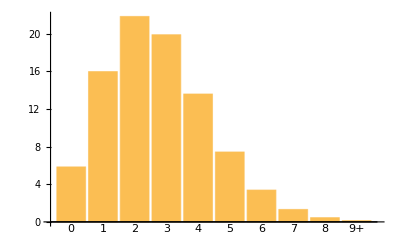

```mathematica
BarO= {8,16,22,18,11,7,5,2,0,1};
BarE= ExpectedE;
BarChart[BarO,ChartLabels->{"0","1","2","3","4","5","6","7","8","9+"}]
BarChart[BarE,ChartLabels->{"0","1","2","3","4","5","6","7","8","9+"}]
```